```mathematica
mp=0.938272046;(*GeV/c^2*)
mn=1.00137842*mp(*GeV/c^2*);
M=2*mp+2*mn;
m=M/4;
ℏc=0.19732697178(*Giga ElectronVolt*Femto Meter*);
r=.535^(-1/2)(*Femto Meter*);
B=1/4*r^2/ℏc^2(*(c/GeV)^2*);
A=4;
```

```mathematica
En=.100(*GeV*);
EnL=En+mp;
s=mp^2+M^2+2*M*EnL;
ϵ=EnL/(M/Sqrt[s]);
P=Sqrt[EnL^2-mp^2];
k=P*(M/Sqrt[s]);
s2=mp^2+m^2+2*m*EnL;
ϵ2=EnL*(m/Sqrt[s2]);
κ=P*(m/Sqrt[s2]);
ηO=(1-ϵ/M)*(mp+M)/Sqrt[s];
ηD=(1-ϵ/ϵ2+(A-1)*ϵ/M)*(mp+M)/Sqrt[s];
```

```mathematica
pp100a=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/Users/Micah/Documents/JerryDuty/eikexp/pp100b.csv"];
```

```mathematica
(*pp100a=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100a.csv"];
pp100b=Import["/phys/users/mbuuck/JerryDuty/eikexp/pp100b.csv"];*)
```

```mathematica
pp100a=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+I*pp100a[[All,3]]}];
pp100b=Transpose[{pp100b[[All,1]],pp100b[[All,2]]+I*pp100b[[All,3]]}];
```

```mathematica
θpp100=Transpose[{pp100a[[All,1]],pp100a[[All,2]]+pp100b[[All,2]]}];
```

```mathematica
θtoq[x_]:={2 Sqrt[En^2+2*En*m] Sin[x[[1]] Pi/360],x[[2]]}
```

```mathematica
pp100=θtoq/@θpp100;
```

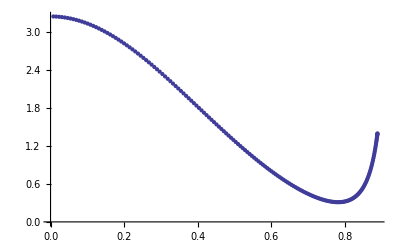

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Re[pp100[[All,2]]]}]]
```

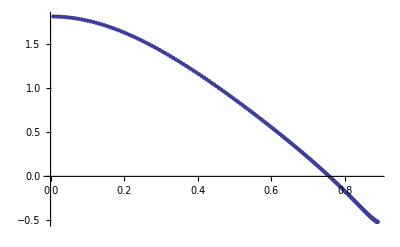

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Im[pp100[[All,2]]]}]]
```

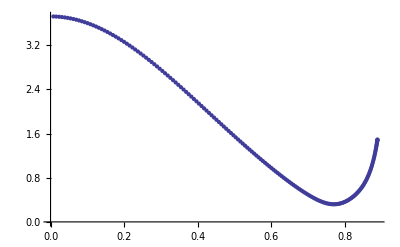

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Abs[pp100[[All,2]]]}]]
```

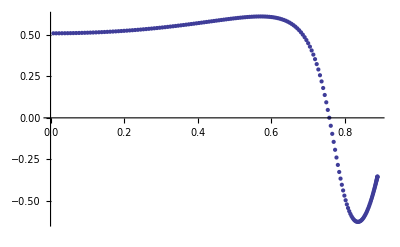

```mathematica
ListPlot[Transpose[{pp100[[All,1]],Arg[pp100[[All,2]]]}]]
```

{σ→216.167,βre→3.34766}

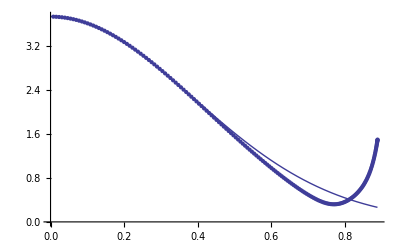

```mathematica
Npts=50;
FindFit[Transpose[{pp100[[1;;Npts,1]],Abs[pp100[[1;;Npts,2]]]}],κ σ/(4 Pi) Exp[-βre q^2],{σ,βre},q]
Show[Plot[κ σ/(4 Pi) Exp[-βre q^2]/.%,{q,0,2 P}],ListPlot[Transpose[{pp100[[All,1]],Abs[pp100[[All,2]]]}]]]
```

{ρ→1.79511,βim→-0.382555}

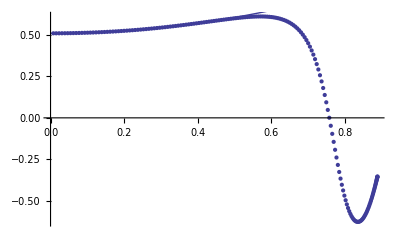

```mathematica
FindFit[Transpose[{pp100[[1;;Npts,1]],Arg[pp100[[1;;Npts,2]]]}],ArcTan[ρ,1]-βim q^2,{ρ,βim},q]
Show[ListPlot[Transpose[{pp100[[All,1]],Arg[pp100[[All,2]]]}]],Plot[ArcTan[ρ,1]-βim q^2/.%,{q,0,2 P}]]
```

```mathematica
σ=216.16725898232463;
ρ=1.7951093517987904;
β=3.34766095571194-I 0.38255457506481644;
```

## Glauber

The data below is pulled directly from Wallace's lecture in Advances in Nuclear Physics:

```mathematica
σ1=σ/(10 ℏc^2) (1-I ρ)/(8 Pi β)
Fcm[q_]:=Exp[B*q^2/A]
```

7.84941-10.9478 ⅈ

```mathematica
F0[q_]:=-2*I*k*Fcm[q]*(B+β)*Sum[Binomial[A,j]/j*(-σ (1-I ρ)/(8 Pi (B+β)))^j*Exp[-(B+β)*q^2/j],{j,1,A}]*ℏc
```

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
```

366.467

## Add in First Order Correction

```mathematica
Γ[b_]:=σ1 Exp[-b^2/(4 β)]
```

```mathematica
Γ[0]
```

7.84941-10.9478 ⅈ

```mathematica
U[q_]:=2*Pi*I*NIntegrate[b*BesselJ[0,b*q]*Log[1-Γ[b]],{b,0,Infinity}]
```

```mathematica
U[0]
```

-229.677+139.815 ⅈ

Wallace parameterizes it as a gaussian in q, so we should check the validity of that assertion:

```mathematica
Quiet[Table[{q,Abs[U[Sqrt[q]]]},{q,0.001,1.001,.1}]]
```

{{0.001,267.601},{0.101,163.447},{0.201,96.9403},{0.301,56.142},{0.401,32.9754},{0.501,21.7229},{0.601,17.2635},{0.701,15.2662},{0.801,13.657},{0.901,11.973},{1.001,10.2844}}

```mathematica
interp1=Interpolation[{{0.001,267.6009711362816},{0.101,163.44675971176866},{0.201,96.94030428880455},{0.30100000000000005,56.14197444395826},{0.401,32.97539756633726},{0.501,21.722936647060653},{0.6010000000000001,17.26350374121591},{0.7010000000000001,15.266239284659598},{0.801,13.656986130491413},{0.901,11.97303259051124},{1.001,10.284363090156685}}];
```

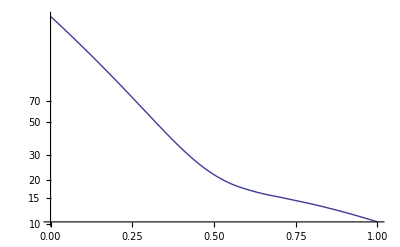

```mathematica
Quiet[LogPlot[interp1[t],{t,0,1}]]
```

The magnitude seems to be well approximated by a gaussian.

```mathematica
Quiet[Table[{q,Arg[U[Sqrt[q]]]},{q,0.001,1.001,.1}]]
```

{{0.001,2.59369},{0.101,2.46789},{0.201,2.29231},{0.301,2.0362},{0.401,1.65631},{0.501,1.14854},{0.601,0.633289},{0.701,0.222458},{0.801,-0.0958621},{0.901,-0.366557},{1.001,-0.621017}}

```mathematica
interp2=Interpolation[{{0.001,2.593693233104296},{0.101,2.4678862090660036},{0.201,2.292311057919859},{0.30100000000000005,2.0362023477723437},{0.401,1.6563089912578193},{0.501,1.148539978612237},{0.6010000000000001,0.6332890412921269},{0.7010000000000001,0.22245848647942978},{0.801,-0.09586213596641777},{0.901,-0.36655685940349675},{1.001,-0.6210165292852018}}];
```

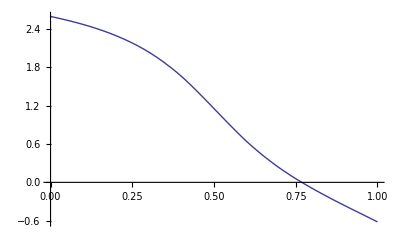

```mathematica
Quiet[Plot[interp2[t],{t,0,1}]]
```

```mathematica
Quiet[U[.1]]
```

-217.445+135.634 ⅈ

```mathematica
γ=100*Quiet[(Log[U[0]]-Log[U[0.1]])]
```

4.80191+1.08846 ⅈ

```mathematica
Z=U[0]/(-I*4*Pi*σ1*β)(*Unitless*)
```

0.232481-0.4101 ⅈ

Here are a bunch of parameters that Wallace has defined in his paper.

```mathematica
γ1:=γ*β/(γ+β)(*(c/GeV)^2*)
αnL[n_,L_]:=If[n==1,(2*(γ+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ+B)^-1+(γ1+B)^-1+L*(β+B)^-1)^-1,If[n==3,(2*(γ1+B)^-1+L*(β+B)^-1)^-1]]]
an[n_]:=If[n==1,(γ+B)^-2,If[n==2,-2*σ1*(γ1/γ)*(γ+B)^-1*(γ1+B)^-1,If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-2]]]
bn[n_]:=If[n==1,(γ+B)^-3,If[n==2,-σ1*(γ1/γ)*(γ1+B)^-1*(γ+B)^-1*((1-B*γ1/(β*(B+γ1)))/(γ+B)+(1-γ1/β)/(γ1+B)),If[n==3,σ1^2*(γ1/γ)^2*(γ1+B)^-3*(1-B*γ1/(β*(B+γ1)))*(1-γ1/β)]]]
γ2:=γ*β/(β+2*γ)(*(c/GeV)^2*)
βnL[n_,L_]:=If[n==1,((γ/2+B)^-1+L*(β+B)^-1)^-1,If[n==2,((γ2/2+B)^-1+L*(β+B)^-1)^-1]]
cn[n_]:=If[n==1,(γ-2*B)*(γ+2*B)^-2,If[n==2,-σ1(γ2/γ1)*(γ2+2*B)^-1*(1-2*γ2/γ+2*(γ2)^2/(γ*(γ2+2*B)))]]
dn[n_]:=If[n==1,γ*(γ+2*B)^-3,If[n==2,
-σ1*(γ)^-2*(γ2/(γ2+2*B))^3]]
```

```mathematica
FO1[q_(*c/GeV*)]:=A*(A-1)*Fcm[q]*ηO*(β*σ1*Z)^2/(2*(2*Pi*(B+β))^(1/2))*Sum[Binomial[A-2,L]*(-σ1*β/(B+β))^L*Sum[αnL[n,L]*(an[n]-4*αnL[n,L]*bn[n]*(1-αnL[n,L]q^2))*Exp[-αnL[n,L]*q^2],{n,1,3}],{L,0,A-2}]*ℏc
```

```mathematica
FD1[q_(*c/GeV*)]:=A*Fcm[q]*ηD*(β*σ1*Z)^2/(2*γ*Sqrt[2*Pi*γ])*Sum[Binomial[A-1,L]*(-σ1*β/(B+β))^L*Sum[βnL[n,L]*(cn[n]-4*βnL[n,L]*dn[n]*(1-βnL[n,L]*q^2))*Exp[-βnL[n,L]*q^2],{n,1,2}],{L,0,A-1}]*ℏc
```

```mathematica
Im[FO1[0]+FD1[0]]/Im[F0[0]+FO1[0]+FD1[0]]
```

0.657635

```mathematica
40*Pi/(k/ℏc) Im[F0[0]]
40*Pi/(k/ℏc) Im[FO1[0]+FD1[0]]
```

366.467

703.931

```mathematica
FO1[0]
```

-101.858+21.8888 ⅈ

```mathematica
FD1[0]
```

38.6648-11.9586 ⅈ